### 1D Free Electron

```mathematica
ClearAll["Global`*"]
σ0={{1, 0}, {0, 1}} ;σ1={{0, 1}, {1, 0}};σ2={{0, -ⅈ}, {ⅈ, 0}};σ3={{1, 0}, {0, -1}};
```

#### Spinless case

(*=== Ψ_DW=(s,s)^T ===*)

```mathematica
TRS0=σ1;
SIS0=σ1;
TRS=TRS0;
SIS=SIS0;
```

Check Symmetries of DW Hamiltonian

```mathematica
HDW0={{(k+q)^2, 0}, {0, (k-q)^2}};
delHDW0sis=(Inverse[SIS].HDW0.SIS)-(HDW0/.{k->-k});
delHDW0trs=(Inverse[TRS].HDW0.TRS)-(Transpose[HDW0]/.{k->-k});
Print["delHDW0sis=",Simplify[delHDW0sis]//MatrixForm,"; delHDW0trs=",Simplify[delHDW0trs]//MatrixForm]
```

delHDW0sis=(0 | 0
0 | 0); delHDW0trs=(0 | 0
0 | 0)

```mathematica
HDWep0=a01 σ1+a02 σ2;
HDWep=HDWep0;
```

```mathematica
delHDWepsis=(Inverse[SIS].HDWep.SIS)-(HDWep/.{k->-k});
Simplify[delHDWepsis]//MatrixForm
```

(0 | 2 ⅈ a02
-2 ⅈ a02 | 0)

```mathematica
a02=0;
Simplify[delHDWepsis]//MatrixForm
MatrixForm[HDWep]
```

(0 | 0
0 | 0)

(0 | a01
a01 | 0)

```mathematica
delHDWeptrs=(Inverse[TRS].HDWep.TRS)-(Transpose[HDWep]/.{k->-k});
Simplify[delHDWeptrs]//MatrixForm
```

(0 | 0
0 | 0)

```mathematica
Simplify[HDWep]//MatrixForm
```

(0 | a01
a01 | 0)

#### Spinful case

(*=== Ψ=(s,↑,s,↓,s,↑,s,↓)^T ===*)

```mathematica
TRS1=KroneckerProduct[σ1,ⅈ σ2];
SIS1=KroneckerProduct[σ1,σ0];
C2z = KroneckerProduct[σ0,ⅈ σ3];
TRS=TRS1;
SIS=SIS1;
```

Check Symmetries of DW Hamiltonian

```mathematica
HDW1={{(k+q)^2, 0, 0, 0}, {0, (k+q)^2, 0, 0}, {0, 0, (k-q)^2, 0}, {0, 0, 0, (k-q)^2}};
delHDW1sis=(Inverse[SIS].HDW1.SIS)-(HDW1/.{k->-k});
delHDW1trs=(Inverse[TRS].HDW1.TRS)-(Transpose[HDW1]/.{k->-k});
delHDW1c2z=(Inverse[C2z].HDW1.C2z)-(HDW1/.{k->k});
Print["delHDW1sis=",Simplify[delHDW1sis]//MatrixForm, 
	  "; delHDW1trs=",Simplify[delHDW1trs]//MatrixForm, 
	  "; delHDW1c2z=",Simplify[delHDW1c2z]//MatrixForm]
```

delHDW1sis=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0); delHDW1trs=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0); delHDW1c2z=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
HDWep1=({{0, 0, a11+ⅈ b11, a12+ⅈ b12}, {0, 0, a21+ⅈ b21, a22+ⅈ b22}, {a11-ⅈ b11, a21-ⅈ b21, 0, 0}, {a12-ⅈ b12, a22-ⅈ b22, 0, 0}});
HDWep=HDWep1;
```

```mathematica
delHDWepsis=(Inverse[SIS].HDWep.SIS)-(HDWep/.{k->-k});
Simplify[delHDWepsis]//MatrixForm
```

(0 | 0 | -2 ⅈ b11 | -a12+a21-ⅈ (b12+b21)
0 | 0 | a12-a21-ⅈ (b12+b21) | -2 ⅈ b22
2 ⅈ b11 | a12-a21+ⅈ (b12+b21) | 0 | 0
-a12+a21+ⅈ (b12+b21) | 2 ⅈ b22 | 0 | 0)

```mathematica
b11=0;b22=0;b21=-b12;
a21=a12;
Simplify[delHDWepsis]//MatrixForm
MatrixForm[HDWep]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | a11 | a12+ⅈ b12
0 | 0 | a12-ⅈ b12 | a22
a11 | a12+ⅈ b12 | 0 | 0
a12-ⅈ b12 | a22 | 0 | 0)

```mathematica
delHDW1c2z=(Inverse[C2z].HDWep.C2z)-(HDWep/.{k->k});
delHDW1c2z//MatrixForm
```

(0 | 0 | 0 | -2 a12-2 ⅈ b12
0 | 0 | -2 a12+2 ⅈ b12 | 0
0 | -2 a12-2 ⅈ b12 | 0 | 0
-2 a12+2 ⅈ b12 | 0 | 0 | 0)

```mathematica
a12=0;b12=0;
delHDW1c2z//MatrixForm
HDWep//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | a11 | 0
0 | 0 | 0 | a22
a11 | 0 | 0 | 0
0 | a22 | 0 | 0)

```mathematica
delHDWeptrs=(Inverse[TRS].HDWep.TRS)-(Transpose[HDWep]/.{k->-k});
Simplify[delHDWeptrs]//MatrixForm
```

(0 | 0 | -a11+a22 | 0
0 | 0 | 0 | a11-a22
-a11+a22 | 0 | 0 | 0
0 | a11-a22 | 0 | 0)

```mathematica
a22=a11;
Simplify[delHDWeptrs]//MatrixForm
Simplify[HDWep]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | a11 | 0
0 | 0 | 0 | a11
a11 | 0 | 0 | 0
0 | a11 | 0 | 0)

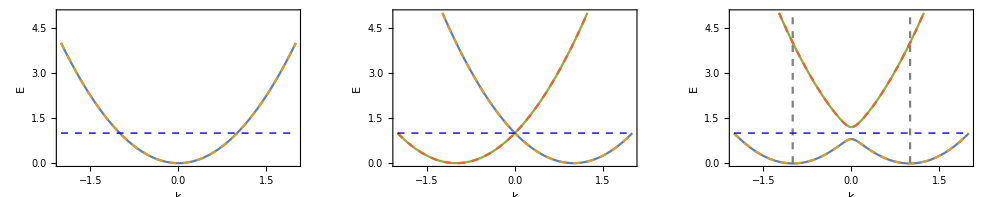

```mathematica
{q,a11}={0,0};
Eigval=Eigenvalues[HDW1+HDWep];
figCDW1=Plot[{Eigval[[1]],Eigval[[3]]},{k,-2,2},Ticks->None,AxesLabel->{"k","E"},PlotRange->{All,{-0.01,5}},Frame->True,PlotTheme->{"ItalicLabels"},PlotStyle->{{},{Dashed}}];

{q,a11}={1,0};
Eigval=Eigenvalues[HDW1+HDWep];
figCDW2=Plot[{Eigval[[1]],Eigval[[2]],Eigval[[3]],Eigval[[4]]},{k,-2,2},AxesLabel->{"k","E"},PlotRange->{All,{-0.01,5}},Frame->True,PlotTheme->{"ItalicLabels"},PlotStyle->{{},{Dashed},{},{Dashed}}];

{q,a11}={1,0.2};
Eigval=Eigenvalues[HDW1+HDWep];
figCDW3=Plot[{Eigval[[1]],Eigval[[2]],Eigval[[3]],Eigval[[4]]},{k,-2,2},Ticks->None,AxesLabel->{"k","E"},PlotRange->{All,{-0.01,5}},Frame->True,PlotTheme->{"ItalicLabels"},PlotStyle->{{},{Dashed},{},{Dashed}}];
Line1=ParametricPlot[{{-q,t},{q,t}},{t,0,5},PlotStyle-> {{Gray,Dashed},{Gray,Dashed}}];
figEF=Plot[q^2,{x,-2,2},PlotStyle-> {Blue,Dashed,Thick}];
figCDW=GraphicsRow[{Show[figCDW1,figEF],Show[figCDW2,figEF],Show[figCDW3,Line1,figEF]}]
```

### 3D Free Electron

(*=== Ψ=(↑,↓,↑,↓)^T ===*)

```mathematica
TRS3=KroneckerProduct[σ1,ⅈ σ2];
SIS3=KroneckerProduct[σ1,σ0];
(*C2z = KroneckerProduct[σ0,ⅈ σ3];*)
TRS=TRS3;
SIS=SIS3;
```

Check Symmetries of DW Hamiltonian

```mathematica
HDW3={{kp km+(kz+q)^2, 0, 0, 0}, {0, kp km+(kz+q)^2, 0, 0}, {0, 0, kp km+(kz-q)^2, 0}, {0, 0, 0, kp km+(kz-q)^2}};
HDWep3=({{0, 0, a11+ⅈ b11, a12+ⅈ b12}, {0, 0, a21+ⅈ b21, a22+ⅈ b22}, {a11-ⅈ b11, a21-ⅈ b21, 0, 0}, {a12-ⅈ b12, a22-ⅈ b22, 0, 0}});;
HDW=HDW3;
HDWep=HDWep3;
delHDWsis=(Inverse[SIS].HDW.SIS)-(HDW/.{kp->-kp,km->-km,kz->-kz});
delHDWtrs=(Inverse[TRS].HDW.TRS)-(Transpose[HDW]/.{kp->-kp,km->-km,kz->-kz});
(*delHDWc2z=(Inverse[C2z].HDW.C2z)-(HDW/.{kp->-kp,km->-km,kz->kz});*)
Print["delHDWsis=",Simplify[delHDWsis]//MatrixForm, 
           "; delHDWtrs=",Simplify[delHDWtrs]//MatrixForm
	]
```

delHDWsis=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0); delHDWtrs=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
delHDWepsis=(Inverse[SIS].HDWep.SIS)-(HDWep/.{kp->-kp,km->-km,kz->-kz});
Collect[Simplify[delHDWepsis],{kp,km}]//MatrixForm
```

(0 | 0 | -2 ⅈ b11 | -a12+a21-ⅈ (b12+b21)
0 | 0 | a12-a21-ⅈ (b12+b21) | -2 ⅈ b22
2 ⅈ b11 | a12-a21+ⅈ (b12+b21) | 0 | 0
-a12+a21+ⅈ (b12+b21) | 2 ⅈ b22 | 0 | 0)

```mathematica
b11=0;b22=0;
a21=a12;b21=-b12;
Print["δHDWepsis==",Simplify[delHDWepsis]//MatrixForm,"; HDWep=",MatrixForm[HDWep]]
```

δHDWepsis==(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0); HDWep=(0 | 0 | a11 | a12+ⅈ b12
0 | 0 | a12-ⅈ b12 | a22
a11 | a12+ⅈ b12 | 0 | 0
a12-ⅈ b12 | a22 | 0 | 0)

```mathematica
delHDWeptrs=(Inverse[TRS].HDWep.TRS)-(Transpose[HDWep]/.{kp->-kp,km->-km,kz->-kz});
Simplify[delHDWeptrs]//MatrixForm
```

(0 | 0 | -a11+a22 | -2 a12+2 ⅈ b12
0 | 0 | -2 (a12+ⅈ b12) | a11-a22
-a11+a22 | -2 a12+2 ⅈ b12 | 0 | 0
-2 (a12+ⅈ b12) | a11-a22 | 0 | 0)

```mathematica
a22=a11;
Simplify[delHDWeptrs]//MatrixForm
```

(0 | 0 | 0 | -2 a12+2 ⅈ b12
0 | 0 | -2 (a12+ⅈ b12) | 0
0 | -2 a12+2 ⅈ b12 | 0 | 0
-2 (a12+ⅈ b12) | 0 | 0 | 0)

```mathematica
Simplify[HDW+HDWep]//MatrixForm
kp=0;km=0;
Simplify[HDW+HDWep]//MatrixForm
```

((kz+q)^2 | 0 | a11 | a12+ⅈ b12
0 | (kz+q)^2 | a12-ⅈ b12 | a11
a11 | a12+ⅈ b12 | (kz-q)^2 | 0
a12-ⅈ b12 | a11 | 0 | (kz-q)^2)

((kz+q)^2 | 0 | a11 | a12+ⅈ b12
0 | (kz+q)^2 | a12-ⅈ b12 | a11
a11 | a12+ⅈ b12 | (kz-q)^2 | 0
a12-ⅈ b12 | a11 | 0 | (kz-q)^2)

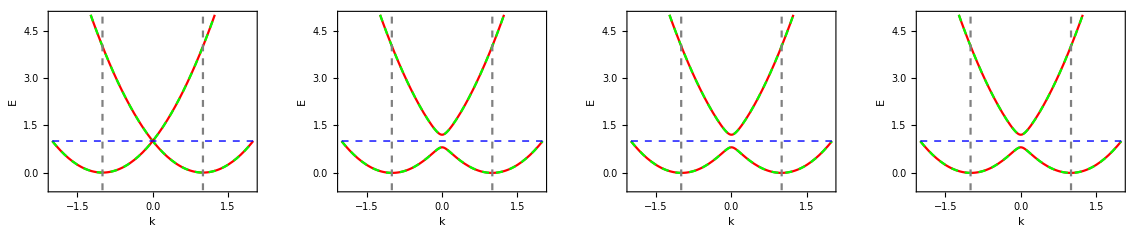

```mathematica
Line1=ParametricPlot[{{-q,t},{q,t}},{t,-1,5},PlotStyle-> {{Gray,Dashed},{Gray,Dashed}}];
figEF=Plot[q^2,{x,-2,2},PlotStyle-> {Blue,Dashed,Thick}];

q=1;
{a11,a12,b12}={0,0,0};
HH=HDW+HDWep;
Eigval=Eigenvalues[HH];
figCDW0=Plot[{Eigval[[1]],Eigval[[2]],Eigval[[3]],Eigval[[4]]},{kz,-2,2},Ticks->None,AxesLabel->{"k","E"},PlotRange->{All,{-0.5,5}},Frame->True,PlotTheme->{"ItalicLabels"},PlotStyle->{{Red},{Green,Dashed},{Red},{Green,Dashed}}];

{a11,a12,b12}={0.2,0,0};
HH=HDW+HDWep;
Eigval=Eigenvalues[HH];
figCDW1=Plot[{Eigval[[1]],Eigval[[2]],Eigval[[3]],Eigval[[4]]},{kz,-2,2},Ticks->None,AxesLabel->{"k","E"},PlotRange->{All,{-0.5,5}},Frame->True,PlotTheme->{"ItalicLabels"},PlotStyle->{{Red},{Green,Dashed},{Red},{Green,Dashed}}];

{a11,a12,b12}={0,0.2,0};
HH=HDW+HDWep;
Eigval=Eigenvalues[HH];
figCDW2=Plot[{Eigval[[1]],Eigval[[2]],Eigval[[3]],Eigval[[4]]},{kz,-2,2},Ticks->None,AxesLabel->{"k","E"},PlotRange->{All,{-0.5,5}},Frame->True,PlotTheme->{"ItalicLabels"},PlotStyle->{{Red},{Green,Dashed},{Red},{Green,Dashed}}];

{a11,a12,b12}={0,0,0.2};
HH=HDW+HDWep;
Eigval=Eigenvalues[HH];
figCDW3=Plot[{Eigval[[1]],Eigval[[2]],Eigval[[3]],Eigval[[4]]},{kz,-2,2},Ticks->None,AxesLabel->{"k","E"},PlotRange->{All,{-0.5,5}},Frame->True,PlotTheme->{"ItalicLabels"},PlotStyle->{{Red},{Green,Dashed},{Red},{Green,Dashed}}];

figCDW=GraphicsRow[{Show[figCDW0,Line1,figEF],Show[figCDW1,Line1,figEF],Show[figCDW3,Line1,figEF],Show[figCDW2,Line1,figEF]}]
```